```mathematica
δai :=−g*σ12r−f−κ*ai;
δar:=g*σ12i−κ*ar;
δp2:=−2*g*(σ12adi)+γc((nc+1)(1−(p2+p1))−nc*p2);
δp1:=2*g*(σ12adi)+γh((nh+1)(1−(p2+p1))−nh*p1);
δ12adi:=g(p2+(p2−p1) *n)−f *σ12r−γh/2 nh*σ12adi−γc/2 nc*σ12adi−κ*σ12adi;
δ12adr:=f *σ12i−γh/2 nh*σ12adr−γc/2 nc*σ12adr−κ*σ12adr;
δ12i:=−g*((p1−p2)*ar)−γc/2 nc*σ12i−γh/2 nh*σ12i;
δ12r:=g((p1−p2)*ai)−γc/2 nc*σ12r−γh/2 nh*σ12r;
δn:=2*g(σ12adi)+2*f *ar+2κ(ncav−n);
```

```mathematica
𝕏:={δai,δar,δp2,δp1,δ12adi,δ12adr,δ12i,δ12r,δn}
```

0

```mathematica
Solve[𝕏==0,{p1,p2,ai,ar,σ12r}]
A=-f/κ
```

{}

-f/κ

```mathematica
x1:=2*g*(σ12r*A)+γc((nc+1)(1−p2-p1)−nc*p2)
x2:=-2*g*(σ12r*A)+γh((nh+1)(1−p2-p1)−nh*p1)
x3:=−γc/2 nc*σ12i−γh/2 nh*σ12i;
x4:=g((p1−p2)*A)−γc/2 *nc*σ12r−γh/2* nh*σ12r;

𝕐:={x1,x2,x3,x4}
```

```mathematica
𝕐
```

{((1+nc) (1-p1-p2)-nc p2) γc+2 A g σ12r,(-nh p1+(1+nh) (1-p1-p2)) γh-2 A g σ12r,-1/2 nc γc σ12i-(nh γh σ12i)/2,A g (p1-p2)-(nc γc σ12r)/2-(nh γh σ12r)/2}

```mathematica
'
```

{((1+nc) (1+p1-p2)-nc p2) γc-2 g (f/κ-(2 f g (1+nc) (nc γc-nh γc) γh κ)/((nc γc+nh γh) (4 f^2 g^2+nc γc γh κ^2+nc^2 γc γh κ^2-nh γc γh κ^2-2 nc nh γc γh κ^2))) σ12r,(-nh p1+(1+nc) (1+p1-p2)) γh+2 g (f/κ-(2 f g (1+nc) (nc γc-nh γc) γh κ)/((nc γc+nh γh) (4 f^2 g^2+nc γc γh κ^2+nc^2 γc γh κ^2-nh γc γh κ^2-2 nc nh γc γh κ^2))) σ12r,-1/2 nc γc σ12i-(nh γh σ12i)/2,g (p1-p2) (f/κ-(2 f g (1+nc) (nc γc-nh γc) γh κ)/((nc γc+nh γh) (4 f^2 g^2+nc γc γh κ^2+nc^2 γc γh κ^2-nh γc γh κ^2-2 nc nh γc γh κ^2)))-(nc γc σ12r)/2-(nh γh σ12r)/2}

```mathematica
FullSimplify[Solve[𝕐==0,{σ12i,σ12r,p1,p2}]]
```

{{σ12i→0,σ12r→(2 f g (-nc+nh) γc γh κ)/(4 f^2 g^2 ((2+3 nc) γc+(2+3 nh) γh)+(nc+nh+3 nc nh) γc γh (nc γc+nh γh) κ^2),p1→(4 f^2 g^2 (γc+nc γc+γh+nh γh)+nc (1+nh) γc γh (nc γc+nh γh) κ^2)/(4 f^2 g^2 ((2+3 nc) γc+(2+3 nh) γh)+(nc+nh+3 nc nh) γc γh (nc γc+nh γh) κ^2),p2→(4 f^2 g^2 (γc+nc γc+γh+nh γh)+(1+nc) nh γc γh (nc γc+nh γh) κ^2)/(4 f^2 g^2 ((2+3 nc) γc+(2+3 nh) γh)+(nc+nh+3 nc nh) γc γh (nc γc+nh γh) κ^2)}}

```mathematica
A2=f/κ-(2 f g (1+nc) (nc γc-nh γc) γh κ)/((nc γc+nh γh) (4 f^2 g^2+nc γc γh κ^2+nc^2 γc γh κ^2-nh γc γh κ^2-2 nc nh γc γh κ^2))*g/κ
```

f/κ-(2 f g^2 (1+nc) (nc γc-nh γc) γh)/((nc γc+nh γh) (4 f^2 g^2+nc γc γh κ^2+nc^2 γc γh κ^2-nh γc γh κ^2-2 nc nh γc γh κ^2))

```mathematica
P1[nh_]:=(((1+nc) (-64 f^6 g^6 (γc+γh) (nc γc+nh γh)^2+16 f^4 g^4 γc γh (nc γc+nh γh) (4 g (1+nc) (nc-nh) (γc+γh)-(nc γc+nh γh) (2 nc^2 (γc+γh)+nc (2 γc-5 nh γc+2 γh-4 nh γh)-nh (2 γc+(2+nh) γh))) κ^2-4 f^2 g^2 γc^2 γh^2 (4 g^2 (1+nc)^2 (nc-nh)^2 (γc+γh)-4 g (1+nc) (nc-nh) (nc+nc^2-nh-2 nc nh) (γc+γh) (nc γc+nh γh)+(nc+nc^2-nh-2 nc nh) (nc γc+nh γh)^2 (nc^2 (γc+γh)+nc (γc-4 nh γc+γh-2 nh γh)-nh (γc+γh+2 nh γh))) κ^4+nh (-nc (1+nc)+nh+2 nc nh)^2 γc^3 γh^3 (nc γc+nh γh)^3 κ^6))/((nc γc+nh γh) (64 f^6 g^6 (nc γc+nh γh)^2-16 f^4 g^4 γc γh (nc γc+nh γh) (4 g (1+nc) (nc-nh)-3 (nc+nc^2-nh-2 nc nh) (nc γc+nh γh)) κ^2+4 f^2 g^2 γc^2 γh^2 (4 g^2 (1+nc)^2 (nc-nh)^2-4 g (1+nc) (nc-nh) (nc+nc^2-nh-2 nc nh) (nc γc+nh γh)+3 (nc+nc^2-nh-2 nc nh)^2 (nc γc+nh γh)^2) κ^4+(nc+nc^2-nh-2 nc nh)^3 γc^3 γh^3 (nc γc+nh γh)^2 κ^6)))
```

```mathematica
P1[nh_]=(((1+nc) (-64 f^6 g^6 (γc+γh) (nc γc+nh γh)^2+16 f^4 g^4 γc γh (nc γc+nh γh) (4 g (1+nc) (nc-nh) (γc+γh)-(nc γc+nh γh) (nc (2+nc-4 nh) γc-2 nh γc+2 nc (1+nc) γh-(2+5 nc) nh γh)) κ^2-4 f^2 g^2 γc^2 γh^2 (4 g^2 (1+nc)^2 (nc-nh)^2 (γc+γh)-4 g (1+nc) (nc-nh) (nc+nc^2-nh-2 nc nh) (γc+γh) (nc γc+nh γh)-(nc+nc^2-nh-2 nc nh) (nc γc+nh γh)^2 ((nh+nc (-1+nc+2 nh)) γc-(nc+nc^2-nh-4 nc nh) γh)) κ^4+nc (nc+nc^2-nh-2 nc nh)^2 γc^3 γh^3 (nc γc+nh γh)^3 κ^6))/((nc γc+nh γh) (64 f^6 g^6 (nc γc+nh γh)^2-16 f^4 g^4 γc γh (nc γc+nh γh) (4 g (1+nc) (nc-nh)-3 (nc+nc^2-nh-2 nc nh) (nc γc+nh γh)) κ^2+4 f^2 g^2 γc^2 γh^2 (4 g^2 (1+nc)^2 (nc-nh)^2-4 g (1+nc) (nc-nh) (nc+nc^2-nh-2 nc nh) (nc γc+nh γh)+3 (nc+nc^2-nh-2 nc nh)^2 (nc γc+nh γh)^2) κ^4+(nc+nc^2-nh-2 nc nh)^3 γc^3 γh^3 (nc γc+nh γh)^2 κ^6)))
```

((1+nc) (-64 f^6 g^6 (γc+γh) (nc γc+nh γh)^2+16 f^4 g^4 γc γh (nc γc+nh γh) (4 g (1+nc) (nc-nh) (γc+γh)-(nc γc+nh γh) (nc (2+nc-4 nh) γc-2 nh γc+2 nc (1+nc) γh-(2+5 nc) nh γh)) κ^2-4 f^2 g^2 γc^2 γh^2 (4 g^2 (1+nc)^2 (nc-nh)^2 (γc+γh)-4 g (1+nc) (nc-nh) (nc+nc^2-nh-2 nc nh) (γc+γh) (nc γc+nh γh)-(nc+nc^2-nh-2 nc nh) (nc γc+nh γh)^2 ((nh+nc (-1+nc+2 nh)) γc-(nc+nc^2-nh-4 nc nh) γh)) κ^4+nc (nc+nc^2-nh-2 nc nh)^2 γc^3 γh^3 (nc γc+nh γh)^3 κ^6))/((nc γc+nh γh) (64 f^6 g^6 (nc γc+nh γh)^2-16 f^4 g^4 γc γh (nc γc+nh γh) (4 g (1+nc) (nc-nh)-3 (nc+nc^2-nh-2 nc nh) (nc γc+nh γh)) κ^2+4 f^2 g^2 γc^2 γh^2 (4 g^2 (1+nc)^2 (nc-nh)^2-4 g (1+nc) (nc-nh) (nc+nc^2-nh-2 nc nh) (nc γc+nh γh)+3 (nc+nc^2-nh-2 nc nh)^2 (nc γc+nh γh)^2) κ^4+(nc+nc^2-nh-2 nc nh)^3 γc^3 γh^3 (nc γc+nh γh)^2 κ^6))

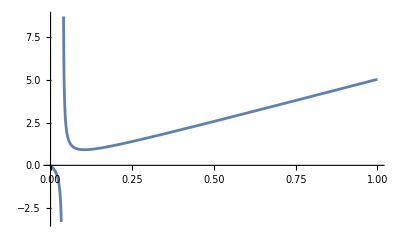

```mathematica
Plot[f/0.2-(2 f 2.8 (1+0) (-11* 1) 1 *0.2)/((+11) (4 f^2 2.8^2+0.1*0.2^2+0.1^2 0.2^2-1   0.2^2-2 0.11 0.2^2)),{f,0,1}]
```

```mathematica
P1[nh_]:=-(-4 f^2 g^2 γc-4 f^2 g^2 nc γc-4 f^2 g^2 γh-4 f^2 g^2 nh γh-nc^2 γc^2 γh κ^2-nc^2 nh γc^2 γh κ^2-nc nh γc γh^2 κ^2-nc nh^2 γc γh^2 κ^2)/(8 f^2 g^2 γc+12 f^2 g^2 nc γc+8 f^2 g^2 γh+12 f^2 g^2 nh γh+nc^2 γc^2 γh κ^2+nc nh γc^2 γh κ^2+3 nc^2 nh γc^2 γh κ^2+nc nh γc γh^2 κ^2+nh^2 γc γh^2 κ^2+3 nc nh^2 γc γh^2 κ^2)
```

```mathematica
P2[nh_]:=(-4 f^2 g^2 γc-4 f^2 g^2 nc γc-4 f^2 g^2 γh-4 f^2 g^2 nh γh-nc nh γc^2 γh κ^2-nc^2 nh γc^2 γh κ^2-nh^2 γc γh^2 κ^2-nc nh^2 γc γh^2 κ^2)/(8 f^2 g^2 γc+12 f^2 g^2 nc γc+8 f^2 g^2 γh+12 f^2 g^2 nh γh+nc^2 γc^2 γh κ^2+nc nh γc^2 γh κ^2+3 nc^2 nh γc^2 γh κ^2+nc nh γc γh^2 κ^2+nh^2 γc γh^2 κ^2+3 nc nh^2 γc γh^2 κ^2)
```

```mathematica
Jh[nh_]:=γh(nh*P1[nh]−(nh+1)*(1-P2[nh]-P1[nh]))
FullSimplify[Jh[nh]]
```

-(2 γh (2 f^2 g^2 ((2+3 nc+nh+2 nc nh) γc+2 (1+nh)^2 γh)+(1+nc) nh (1+nh) γc γh (nc γc+nh γh) κ^2))/(4 f^2 g^2 ((2+3 nc) γc+(2+3 nh) γh)+(nc+nh+3 nc nh) γc γh (nc γc+nh γh) κ^2)

```mathematica
Cancel[((nc-nh) γh (-4 f^2 g^2 (γc-nh γh)+nc nh γc γh (nc γc+nh γh) κ^2))/(4 f^2 g^2 ((2+3 nc) γc+(2+2 nc+nh) γh)+(nc+nc^2+nh+2 nc nh) γc γh (nc γc+nh γh) κ^2)]
```

((nc-nh) γh (-4 f^2 g^2 γc+4 f^2 g^2 nh γh+nc^2 nh γc^2 γh κ^2+nc nh^2 γc γh^2 κ^2))/(8 f^2 g^2 γc+12 f^2 g^2 nc γc+8 f^2 g^2 γh+8 f^2 g^2 nc γh+4 f^2 g^2 nh γh+nc^2 γc^2 γh κ^2+nc^3 γc^2 γh κ^2+nc nh γc^2 γh κ^2+2 nc^2 nh γc^2 γh κ^2+nc nh γc γh^2 κ^2+nc^2 nh γc γh^2 κ^2+nh^2 γc γh^2 κ^2+2 nc nh^2 γc γh^2 κ^2)

```mathematica
Simplify[%69]
```

((nc-nh) γh (-4 f^2 g^2 (γc-nh γh)+nc nh γc γh (nc γc+nh γh) κ^2))/(4 f^2 g^2 ((2+3 nc) γc+(2+2 nc+nh) γh)+(nc+nc^2+nh+2 nc nh) γc γh (nc γc+nh γh) κ^2)

```mathematica
γh=γc=1
g=2.8
κ=0.2
```

1

2.8

0.2

```mathematica
nc=0.02


nh=5
```

0.02

5

```mathematica
0.02
f=0.2
```

0.02

0.2

```mathematica
0.02
```

0.02

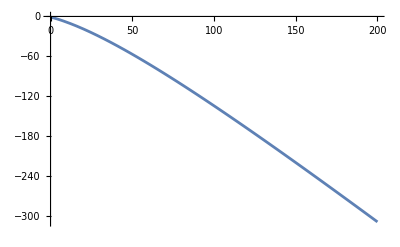

```mathematica
Plot[Jh[nh],{nh,0,200}]
```

```mathematica
Clear[γh,γc,κ,g,nc,f]
Clear[nh]
```

```mathematica
σ12r=(2 f g (-nc+nh) γc γh κ)/(4 f^2 g^2 ((2+3 nc) γc+(2+3 nh) γh)+(nc+nh+3 nc nh) γc γh (nc γc+nh γh) κ^2)
```

(2 f g (-nc+nh) γc γh κ)/(4 f^2 g^2 ((2+3 nc) γc+(2+3 nh) γh)+(nc+nh+3 nc nh) γc γh (nc γc+nh γh) κ^2)

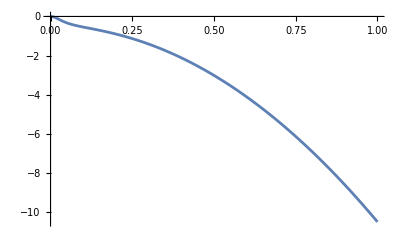

```mathematica
Plot[-4*g*(2 f g (-nc+nh) γc γh κ)/(4 f^2 g^2 ((2+3 nc) γc+(2+3 nh) γh)+(nc+nh+3 nc nh) γc γh (nc γc+nh γh) κ^2)*f/κ-2*f^2/κ,{f,0,1}]
```

```mathematica
FullSimplify[-2*g*(2 f g (-nc+nh) γc γh κ)/(4 f^2 g^2 ((2+3 nc) γc+(2+3 nh) γh)+(nc+nh+3 nc nh) γc γh (nc γc+nh γh) κ^2)*f/κ-f^2/κ]
```

f^2 (-1/κ+(4 g^2 (nc-nh) γc γh)/(4 f^2 g^2 (2 γc+3 nc γc+2 γh+3 nh γh)+(nc+nh+3 nc nh) γc γh (nc γc+nh γh) κ^2))

```mathematica
FortranForm[2*g*(2 f g (-nc+nh) γc γh κ)/(4 f^2 g^2 ((2+3 nc) γc+(2+3 nh) γh)+(nc+nh+3 nc nh) γc γh (nc γc+nh γh) κ^2)*f/κ+2*f^2/κ]
```

(2*f**2)/kappa + (4*f**2*g**2*gammac*gammah*(-nc + nh))/(gammac*gammah*kappa**2*(gammac*nc + gammah*nh)*(nc + nh + 3*nc*nh) + 4*f**2*g**2*(gammac*(2 + 3*nc) + gammah*(2 + 3*nh)))

```mathematica
γh=gammah
γc=gammac
κ=kappa
```

gammah

gammac

kappa